# Bee Thermodynamics

This worksheet take the bee thermodynamic model and reparameterizes it into a dimensionless form.

## The passive model (original formulation and parameterisation)

The thermodynamic heat equation for the passive model is given by

```mathematica
heatEqn = D[Tth, t] == Q/Subscript[m, th]/c;
```

where m_th is the mass of the bee’s thorax (kg), c is the specific heat capacity of the thorax (J kg^-1 K^-1), Tth is the temperature of the thorax (K), and Q is the total rate of heat production by the thorax (J s^-1).

Q can be decomposed into several terms

```mathematica
Q:=Qs + Qr1 - Qr2 - Qc + Qi
```

Qs is the heat from the solar radiation (J s^-1), Qr1 and Qr2 is the incoming and outgoing heat, respectively, from thermal radiation (J s^-1), Qc is the heat loss due to convection (J s^-1) and Qi is the heat from an individual's metabolism (J s^-1).

At equilibrium the right-hand side of the heat equation is zero, meaning the Q=0, and therefore the four terms of Q must balance. This means that at thermal equilibrium 

Qs+Qr1+Qi = Qr2+Qc

### Solar Radiation

```mathematica
Qs=Subscript[ϵ, a] Subscript[a, th] P(Subscript[α, point]+Subscript[α, nonpoint] f);
```

Qs is the solar radiation, P is the incoming flux of solar radiation (J s^-1 m^-2), a_th is the surface area of the thorax (roughly 4.5 x 10^-5 m^2) , ϵ_a is the bee’s absorptivity (=0.91), α_point (=0.25) is the fraction of the bee’s surface that is exposed to the solar radiation,  α_nonpoint (=0.5) is the fraction of the bee’s surface that is exposed to non point sources of solar radiation, and f (=0.25) is the fraction of solar radiation that is reflected from the surface of the Earth.

### Thermal Radiation

Qr1 and Qr2 are the thermal radiation terms which correspond to incoming radiation from the atmosphere, the ground

```mathematica
Qr1 = Subscript[α, nonpoint] Subscript[ϵ, a] Subscript[a, th](δ Tair^6+σ Tg^4);
```

and outgoing radiation from the bee

```mathematica
Qr2=Subscript[ϵ, e] σ Subscript[a, th] Tth^4;
```

where α_nonpoint (=0.5) is the fraction of the bee’s surface that is exposed to non point sources of solar radiation , Tair is the temperature of the air, Tg is the temperature of the ground, Tth is the temperature of the bee’s thorax (all temperature are in Kelvin), σ is the Stefan-Boltzmann constant (=5.67x 10^-8 J s^-1 m^-2 K^-4), δ is a constant still to be full described (= 5.31x 10^-13 J s^-1 m^-2 K^-6), and ϵ_e=0.97 is the emissivity of honeybee.

### Convection

```mathematica
Qc=Subscript[a, th] h(s Tth-Tair);
```

where h (J s^-1 m^-2 K^-1) is a constant that depends upon the environmental conditions  h := c_d κ / d_th (v d_th/ν)^n

and κ is the thermal conductivity of the air (J s^-1 m^-1 K^-1), ν is the kinematic viscosity of the air, d_th is the average diameter of the thorax (m),  and n, c_dare unitless constants estimated from data (for bumblebees n=1.975485 (unitless) and c_d=2.429809 x10^-7 (unitless needs checking)).

### Metabolism

An individuals metabolic rate is a function of body mass and body temperature.

```mathematica
Qi = Subscript[a, met] Exp[-Subscript[b, met] (1/Tth - 1/T0)];
```

where a_met = i0 (m_b/m0)^(3/4) , b_met=Eact/k and i0 is a normalisation constant (the metabolic rate at temperature T0 and weight m0), m_b is the body mass of the bee, Eact =0.63 eV (= 1.0093 × 10^-19 J ) is the activation energy, k is Boltzmann’s constant (=8.617 x 10^-5 eV K^-1 =  1.3806 x 10^-23 J K^-1) and Tth is the temperature of the thorax (K).

### Abdomen Cooling

Bumblebees cool by shunting heat from the thorax to the abdomen.

```mathematica
Qab = r(Tth-Tair)(1/(1+exp(-2(Tth-Tm)));
```

where r is the rate of abdomen cooling in J/s/degree C and Tm is the midpoint of thorax temperature at which abdomen cooling should begin

### Parameterisation

Set some parameter values for a  bee (some of these values need to be reviewed. i0 in particular needs finalising)

```mathematica
(* Most of the parameters or relationships are set here *)
params={ Subscript[m, b]-> 0.149 10^-3,(* Mass of bee, kg *)
Subscript[m, th]->0.057 10^-3, (* Mass of thorax, kg *)
δ-> 5.31 10^-13,  (* Default value 5.31 E-13 *)
f-> 0.25,             (* dimensionless *)
Subscript[α, nonpoint]-> 0.5 ,        (* dimensionless *)
Subscript[α, point]-> 0.25 ,        (* dimensionless *)
c-> 3.349 10^3, (* Specific heat capacity of bee tissue   J K^-1 kg^-1  *)
Subscript[a, th]->9.3896 10^-5,  (* Surface area of the thorax default value 9.3896 E-5 , m^-2*)
Subscript[ϵ, e]-> 0.97,          (* Emissivity of the thorax    dimensionless *)
Subscript[ϵ, a]-> 0.935,         (* Absorptivity of the thorax   dimensionless *)
n-> 1.975,         (* dimensionless *)
v->3.1,              (* Wind speed m s^-1  *)
Subscript[c, d]-> 2.43 10^-7,          (* dimensionless *)
Subscript[d, th]-> 2 (Subscript[a, th]/π)^(1/2),  (* diameter of thorax  m  *)
i0->0.06229515, (* Metabolic power (W = J s^-1) of a bee of mass m0 at temp T0 (about 0.5 W per g)  *)
 m0->0.177 10^-3 ,  (* reference Mass [kg] of a full bee 177 mg *)
 T0 -> 25+ 273.15 ,    (* Temperature for metabolic rate corresponding to i0  *)
τ-> 1,                       (* Time scale, s *)          
Eact-> 0.4*1.602 10^-19 ,        (* Activation energy Joules. Default 0.63 eV, range roughly 0.4-0.7 eV *)
s -> 0.9  ,    (* ratio of surface temperature to internal temperature (thorax) *)
r ->  0.0041,  (* rate of abdomen cooling, J/s/C *)
Tm -> 42+273.15  (* midpoint for abdomen cooling function *)
};
```

```mathematica
constants ={
k-> 1.3806 10^-23, (* Boltzmann constant  J K^-1 *)
σ-> 5.67 10^-8      (* Stefan-Boltzmann constant W m^-2 K^-4 *)
};
```

Set environmental values

```mathematica
(* Now the environmental parameters *)
envParams={
Tair-> 13.468568862777776+273.15,  (* Kelvin *)
Tg-> 17.1+273.15,       (* Kelvin *)
P-> 332.3878,             (*  W m^-2 *)
κ-> (0.02646 Tair^1.5) /(Tair + 245.4 10^(-12/Tair)) ,    (* Thermal conductivity of air  J s^-1 m^-2 K^-1  *)
ν-> (1.458 10^-6  Tair^1.5)/(Tair+110.4)(* Kinematic viscosity m^2 s^-1   *)
};
```

## Non-dimensional version of the passive model

Here we rewrite the model in terms of non-dimensional quantities.

All temperatures will be w.r.t. a reference temp T0, and a timescale τ

#### Heat equation

```mathematica
heatEqnND := x'[y] == Q2;
```

the dimensionless variables are

```mathematica
heatEqnVars = {x->Tth/T0,
y->t/τ}
```

{x→Tth/T0,y→t/τ}

and the terms Q2 is

```mathematica
Q2 := QiND+QsND;
```

#### Metabolic heat production (Qi term)

```mathematica
QiND = K1 Exp[-K2 (1/x - 1)];
```

#### Direct solar radiation, thermal radiation and convection

```mathematica
QsND=K3 + K4 x + K5 x^4;
```

the dimensionless constants are

```mathematica
QParams={
K1-> i0 (Subscript[m, b]/m0)^(3/4)τ/(T0 Subscript[m, th] c), (* Metabolic part *)
K2->Eact/k/T0,  (* Metabolic part *)
K3->Subscript[a, th] (Subscript[ϵ, a](Subscript[α, point] P + Subscript[α, nonpoint](P f + δ Tair^6+σ Tg^4))/T0 + Subscript[c, d] κ (v/ν)^n (Subscript[d, th])^(n-1) (Tair/T0)) τ/(Subscript[m, th] c), (* Mixture of parts *)
K4-> -Subscript[a, th] Subscript[c, d] κ (v/ν)^n (Subscript[d, th])^(n-1) s τ/(Subscript[m, th] c), (* Convection part *)
K5->-Subscript[ϵ, e]σ Subscript[a, th] τ T0^3/( Subscript[m, th] c)     (* Thermal radiation part  *)
};
```

```mathematica
{K1->(i0 τ (Subscript[m, b]/m0)^(3/4))/(T0 c Subscript[m, th]),K2->Eact/(k T0),K3->(τ Subscript[a, th] ((Tair κ (v/ν)^n Subscript[c, d] Subscript[d, th]^(-1+n))/T0+(Subscript[ϵ, a](Subscript[α, point] P + Subscript[α, nonpoint](Pf + δ Tair^6+σ Tg^4)))/T0))/(c Subscript[m, th]),K4->-(κ (v/ν)^n τ Subscript[a, th] Subscript[c, d] Subscript[d, th]^(-1+n))/(c Subscript[m, th]),K5->-(T0^3 σ τ Subscript[a, th] Subscript[ϵ, e])/(c Subscript[m, th])}
```

{K1→(i0 τ (m_b/m0)^(3/4))/(c T0 m_th),K2→Eact/(k T0),K3→(τ a_th ((Tair κ (v/ν)^n c_d d_th^(-1+n))/T0+(((Pf+Tair^6 δ+Tg^4 σ) α_nonpoint+P α_point) ϵ_a)/T0))/(c m_th),K4→-(κ (v/ν)^n τ a_th c_d d_th^(-1+n))/(c m_th),K5→-(T0^3 σ τ a_th ϵ_e)/(c m_th)}

Display the final non-dimensional version of the model.

```mathematica
heatEqnND
```

x'[y]==ⅇ^(-K2 (-1+1/x)) K1+K3+K4 x+K5 x^4

Note: one further parameter could be removed (one of K1, K3, K4 and K5) by scaling the time scale appropriately.

## Numerical solution of the heat equation

### Numerical integration

Define differential equation

```mathematica
eqn1 =Q2/.{x->x[y]}/.QParams //.params /.constants//.envParams ;
eqn := x'[y]==eqn1;
eqn
```

x'[y]==0.00866345+0.00096192 ⅇ^(-15.5675 (-1+1/x[y]))-0.00742766 x[y]-0.000716995 x[y]^4

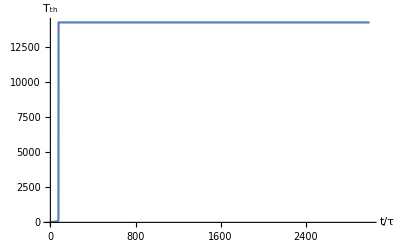

```mathematica
sol=NDSolve[{eqn,x[0]==1},x,{y,0,5000}, Method-> "Automatic"];
Plot[Evaluate[x[y]*T0-273.15/.sol/.params],{y,0,3000},PlotRange->All, AxesLabel->{t/τ, Subscript[T, th]}]
```

### Numerically solve for equilibrium

Now numerically solve for the equilibrium value

```mathematica
Qsub = Q2 /.QParams//.params//.envParams/.constants
xEquilib = NSolve[Qsub==0, x, Reals]
```

0.00866345+0.00096192 ⅇ^(-15.5675 (-1+1/x))-0.00742766 x-0.000716995 x^4

{{x→-56.5003},{x→48.6859}}

Write equilibria in degrees C

```mathematica
x*T0 - 273.15 /. xEquilib/.params
```

{-17118.7,14242.5}

### Stability of the equilibria

Calculate the derivative of Q2 w.r.t. x at the equilibrium value. 

For the solution to be stable this should be negative

```mathematica
D[Q2,x]/.xEquilib /.QParams//.params//.envParams/.constants
```

{552.906,-304.515}

## Sensitivity Analysis of Equilibrium

TthEquilib solves the equation
        Q = 0
 for Tth.  
 
 The sensitivity is d T_th / d x  where x is some parameter.    
 
 By the chain rule
 d Q / d x  =   d Q / d T_th .  d T_th/d x     
 where the derivatives are partial derivatives.   
 
 Evaluating each derivative at the equilibrium Tth we have
        d T_th/ d x = (d Q / d x)  / (d Q / d T_th)

 
Partially differentiate Q w.r.t. each parameter (dQ1) and Q w.r.t. Tth (dQ2). The sensitivity of TthEquilib to the parameter is dQ1/dQ2 evaluated at TthEquilib.

Create a list of all the parameters to include in the analysis

```mathematica
sParams = {K1,K2,K3,K4,K5};
```

Calculate the sensitivity of Tth to each parameter in turn

```mathematica
solution = 2;
sub= xEquilib[[solution]] ; (* pick the second equilibrium point *)Do[Print[{sParams[[i]],-D[Q2,sParams[[i]]]/D[Q2,x]/.QParams//.params/.constants//.envParams /. sub}],{i,1,Length[sParams]}]
```

{K1,13753.6}

{K2,12.9582}

{K3,0.00328391}

{K4,0.15988}

{K5,18450.3}

Calculate elasticities of Tth to each parameter (i.e. percentage change for percentage change in parameter)

```mathematica
Do[Print[{sParams[[i]],-D[Q2,sParams[[i]]]/D[Q2,x]sParams[[i]]/x/.QParams//.params/.constants//.envParams /. sub}],{i,1,Length[sParams]}]
```

{K1,0.27174}

{K2,4.14344}

{K3,5.84358×10^-7}

{K4,-0.0000243918}

{K5,-0.271716}

#### Test sensitivity calculation

Change by K2 parameter by a little and recalculate equilibrium

```mathematica
QParamsPerturb:={
K1-> i0 (Subscript[m, b]/m0)^(3/4)τ/(T0 Subscript[m, th] Subscript[c, k]), (* Metabolic part *)
K2->Eact/k/T0 + 1,  (* Metabolic part *)
K3->(Subscript[ϵ, a] Subscript[f, bee] (1+f)(P + δ Tair^6+σ Tg^4)/T0 + Subscript[c, d] κ (v/ν)^n (Subscript[d, th])^(n-1) (Tair/T0)) Subscript[a, th] τ/(Subscript[m, th] Subscript[c, k]), (* Mixture of parts *)
K4-> -Subscript[a, th] Subscript[c, d] κ (v/ν)^n (Subscript[d, th])^(n-1) τ/(Subscript[m, th] Subscript[c, k]), (* Conduction part *)
K5->-Subscript[ϵ, e]σ Subscript[a, th] τ T0^3/( Subscript[m, th] Subscript[c, k])     (* Thermal radiation part  *)
}
```

Numerical solve for the perturbed parameters

```mathematica
QsubPerturb = Q2 /.QParamsPerturb//.params/.envParams/.constants;
xEquilibPerturb = NSolve[QsubPerturb==0, x, Reals];
```

Calculate sensitivity empirically

```mathematica
( x/.xEquilibPerturb[[solution]])-(x/.xEquilib[[solution]])
```

ReplaceAll::reps: {x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-48.6859+(x/.x)

Compare to analytical

```mathematica
Print[{K2,-D[Q2,K2]/D[Q2,x]/.QParams//.params/.constants/.envParams /. sub}]
```

{K2,-3945.96/(-304.508-(0.109427 Tair^1.5 ((110.4+Tair)/Tair^1.5)^1.975)/(245.4 10^(-12/Tair)+Tair))}